Power::infy: Infinite expression 1/0. encountered.

Indeterminate

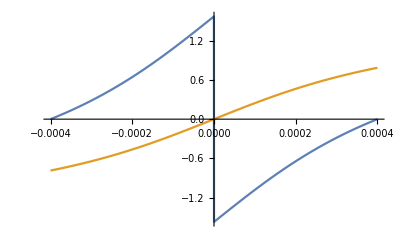

0.0000144347

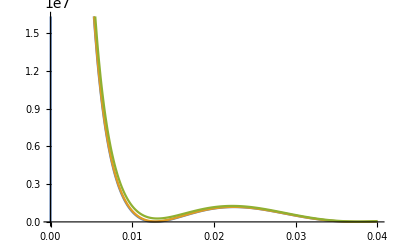

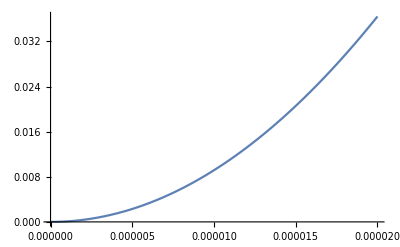

NIntegrate::inumr: The integrand 0.000184835\ ⅇ^-7.10754×10^-8/lambda\ (ⅇ^π^2/1953125000000000\ lambda^2 - Sin[0.000177688\ theta/lambda - ArcTan[Times[« 7 »]]])/lambda\ (1/6250000 + theta^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{3/10000000, 7/10000000}}.

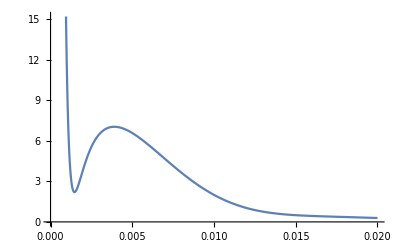

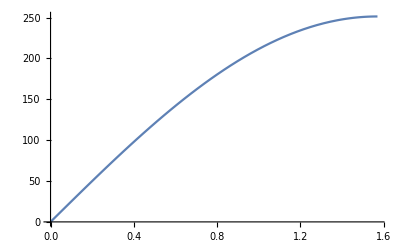

```mathematica
gamma=2500;
eps1=1;
eps2=11.9;
eps3=250;
c=299792458;
hbar=1.05457173*^-34;
beta=Sqrt[1-1/gamma^2];
e=1.602*^-19;
n=2*^10;(*number of electrons*)
q=n*e;(*bunch charge in Coulombs*)
rad=0.02 ;(*lense diameter in m*)
d=0.05 ;(*distance from foil to lens in m*)
a=0.000028280000000; (*size of diffraction slit in m*)
lowerlambda=300*^-9;(*Visible Spectrum m*)
averagelambda=500*^-9;
upperlambda=700*^-9;
eps0=8.854*^-12;
sigx=20*^-6;
sigy=sigx;
sigz=20*^-6;
alpha=7.297*^-3;
theta0=Pi/4;

thetalens=ArcTan[a/(2*d)];
thetamax=1/gamma;

k[lambda_]:=
2*Pi/lambda
kx[lambda_,theta_,phi_]:=
k[lambda]*Sin[theta]*Cos[phi]
ky[lambda_,theta_,phi_]:=
k[lambda]*Sin[theta]*Sin[phi]
Eta[lambda_]:=
k[lambda]/(beta*gamma)
f[lambda_,theta_,phi_]:=
Sqrt[kx[lambda,theta,phi]^2+Eta[lambda]^2]

f1[lambda_,theta_,phi_]:=
(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)/(-2*f[lambda,theta,phi]*ky[lambda,theta,phi])

Phi[lambda_,theta_,phi_]:=
ArcTan[(f[lambda,theta,phi]^2-ky[lambda,theta,phi]^2)/(-2*f[lambda,theta,phi]*ky[lambda,theta,phi])]
(*(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)/(-2*f[lambda,theta,phi]*ky[lambda,theta,phi])*)

Phi2[lambda_,thetax_,thetay_]:=
ArcTan[thetay/Sqrt[1/gamma^2+thetax^2]]

Nsingle[lambda_,theta_,phi_,y_,a_]:=
1/2*alpha/lambda^3*Exp[-a*f[lambda,theta,phi]]/(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)*(Exp[2*y*f[lambda,theta,phi]]+Exp[-2*y*f[lambda,theta,phi]]-2*Sin[a*ky[lambda,theta,phi]+Phi[lambda,theta,phi]])

Nbunch[lambda_,theta_,phi_,y0_,a_]:=
1/2*alpha/lambda^3*Exp[-a*f[lambda,theta,phi]]/(f[lambda,theta,phi]^2+ky[lambda,theta,phi]^2)*(Exp[2*f[lambda,theta,phi]^2*sigy^2]*(Exp[2*y0*f[lambda,theta,phi]]+Exp[-2*y0*f[lambda,theta,phi]])-2*Sin[a*ky[lambda,theta,phi]+Phi[lambda,theta,phi]])

NbunchPlane[lambda_,theta_,phi_,a_]:=
alpha/(4*Pi^2)*1/lambda*Exp[-2*Pi*a/(gamma*lambda)]/(theta^2+1/gamma^2)*(Exp[8*Pi^2*sigy^2/(gamma*lambda)^2]-Sin[2*Pi*a*theta/lambda+Phi[lambda,theta,phi]])

Test[lambda_,theta_,phi_,a_,sigy_]:=
alpha/(4*Pi^2)*1/lambda*Exp[-2*Pi*a/(gamma*lambda)]/(theta^2+1/gamma^2)*(Exp[8*Pi^2*sigy^2/(gamma*lambda)^2]-Sin[2*Pi*a*theta/lambda+Phi[lambda,theta,phi]])

Test2[lambda_,thetax_,thetay_,a_,sigy_]:=
alpha/(4*Pi^2)*1/lambda*Exp[-2*Pi*a*Sin[theta0]*Sqrt[1/gamma^2+thetax^2]/(lambda)]/(thetax^2+thetay^2+1/gamma^2)*(Exp[8*Pi^2*sigy^2/(lambda)^2*(1/gamma^2+thetax^2)]-Cos[2*Pi*a*Sin[theta0]*thetay/lambda+2*Phi2[lambda,thetax,thetay]])

NbunchPlane[averagelambda,0.00000,Pi/2,a]
(*NIntegrate[Sin[theta]*Nsingle[lambda,theta,phi,0],{theta,0,Pi/2},{phi,0,2*Pi},{lambda,300*^-9,700*^-9}]*)
(*DensityPlot[Nbunch[500*^-9,theta,phi,0],{theta,-Pi/2,Pi/2},{phi,0,2*Pi}]*)
(*Plot[2*Pi*Nsingle[500*^-9,0,theta,0],{theta,0,2*Pi}]*)
Plot[{Phi[500*^-9,theta,Pi/2],Phi2[500*^-9,0,theta]},{theta,-1/gamma,1/gamma}]
(*Plot[{Sin[10/gamma]*Test[averagelambda,10/gamma,Pi/2,a],Sin[100/gamma]*Test[averagelambda,100/gamma,Pi/2,a],Sin[1000/gamma]*Test[averagelambda,1000/gamma,Pi/2,a]},{a,0,0.0001}]*)
NIntegrate[Sin[-thetax+Pi/2]*Test2[lambda,thetax,thetay,a,sigy],{lambda,lowerlambda,upperlambda},{thetax,0,thetalens},{thetay,0,thetalens}]
Plot[{Test2[averagelambda,0,thetay,a,0],Test2[averagelambda,0,thetay,a,20*^-6],Test2[averagelambda,0,thetay,a,50*^-6]},{thetay, 0,100/gamma}]
Plot[Test2[averagelambda,0,0,a,sigy]/Test2[averagelambda,0,1/gamma,a,sigy],{sigy, 0,20*^-6}]
Plot[NIntegrate[NbunchPlane[lambda,theta,Pi/2,a],{lambda,lowerlambda,upperlambda}],{theta,0,50/gamma}]
(*Plot[NIntegrate[Sin[theta]*Nbunch[averagelambda,theta,phi,0,a],{lambda,lowerlambda,upperlambda},(*,{theta,0,Pi/2},*){phi,0,2*Pi},MaxRecursion->12],{theta, 0,1/gamma}]*)
(*Plot[NIntegrate[Sin[theta]*Nsingle[averagelambda,theta,phi,0,a],{lambda,lowerlambda,upperlambda},(*,{theta,0,Pi/2},*){phi,0,2*Pi},{theta,0,Pi/2},MaxRecursion->12],{a,0,0.0001}]*)

Plot[sigy*f[averagelambda,theta,0],{theta,0,Pi/2}]
(*Plot[Nbunch[averagelambda,theta,0,0,a],{theta,0,Pi/2}]*)
```

```mathematica
Indeterminate
```

Indeterminate

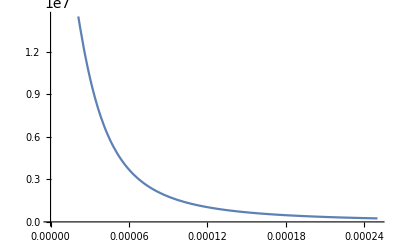

-Graphics-